# Potentials and Fields Near Electric Charge.

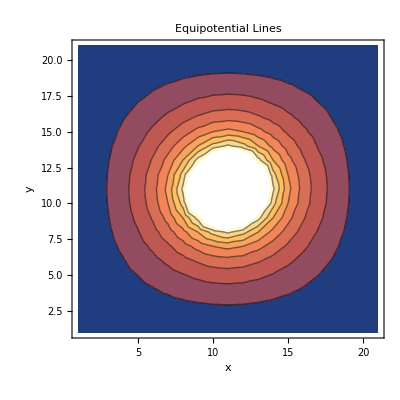

-Graphics3D-

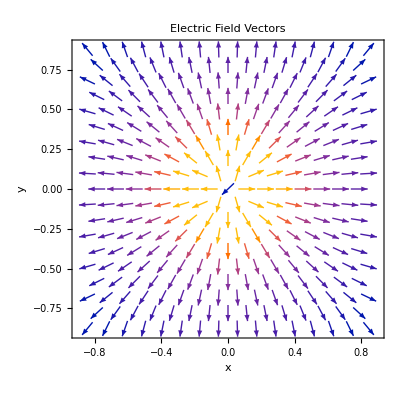

```mathematica
(*Initialization*)
dx=0.1;
dy=dx;
dz=dx;
xmax=1;
xmin=-1;
xlist=Range[xmin,xmax,dx];
ylist=xlist;
zlist=xlist;
lx=Length[xlist];
V=ConstantArray[0,{lx,lx,lx}];
ρ=ConstantArray[0,{lx,lx,lx}];
ρ[[(lx+1)/2,(lx+1)/2,(lx+1)/2]]=1/dx^3;


(*Updating V*)
Vold=V;
tol=1;
k=1;
While[tol>0.00001,Do[Do[Do[V[[i,j,k]]=((1/6)*(V[[i+1,j,k]]+V[[i-1,j,k]]+V[[i,j+1,k]]+V[[i,j-1,k]]+V[[i,j,k+1]]+V[[i,j,k-1]]))+ρ[[i,j,k]]*((dx)^2)/6,{i,2,lx-1}],{j,2,lx-1}],{k,2,lx-1}];
dV=Abs[V-Vold];
tol=Max[dV];
Vold=V;
k=k+1;];
MatrixForm[V];
ListContourPlot[V[[All,All,(lx+1)/2]],AxesLabel->{"x","y"},PlotLabel->"Equipotential Lines"]
ListPlot3D[V[[All,All,(lx+1)/2]],PlotRange->All,AxesLabel->{"x","y","V"},PlotLabel->"3D Potential Surface"]
(***********************************************************)
Ex=0*V; (*we wont calculate the E at the boundaries*)
Do[Ex[[i,j,k]]=-((V[[i+1,j,k]]-V[[i-1,j,k]])/(2 dx)),{j,2,lx-1},{i,2,lx-1},{k,2,lx-1}];
MatrixForm[Ex];
Ey=0*V; (*we wont calculate the E at the boundaries*)
Do[Ey[[i,j,k]]=-((V[[i,j+1,k]]-V[[i,j-1,k]])/(2 dy)),{j,2,lx-1},{i,2,lx-1},{k,2,lx-1}];
MatrixForm[Ey];
Ez=0*V; (*we wont calculate the E at the boundaries*)
Do[Ez[[i,j,k]]=-((V[[i,j,k+1]]-V[[i,j,k-1]])/(2 dz)),{j,2,lx-1},{i,2,lx-1},{k,2,lx-1}];
MatrixForm[Ez];
ListVectorPlot[Flatten[Table[{{xlist[[i]],ylist[[j]]},{Ex[[i,j,(lx+1)/2]],Ey[[i,j,(lx+1)/2]]}},{i,2,lx-1},{j,2,lx-1}],1],AxesLabel->{"x","y"},PlotLabel->"Electric Field Vectors"]
```